## thermal conductivity

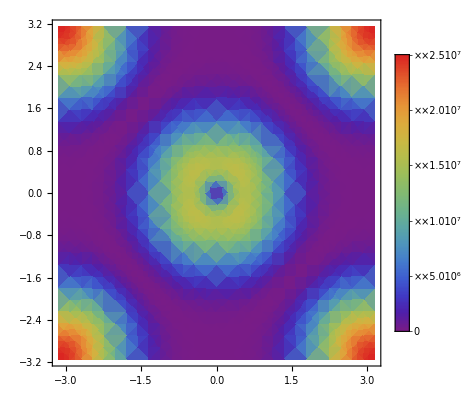

```mathematica
J=1;
z=4;
β=0.01;
ξ=0.001;
ω=1;
b=0.1;
α=0.01;
γ[kx_,ky_]:=2*(Cos[kx]+Cos[ky]);
ϵ[kx_,ky_,b_]:=2J*z*Sqrt[(z+γ[kx,ky])(z+γ[kx,ky]*(2*b^2-1))];
heatconductivitydensity[kx_,ky_,b_,β_,ξ_]:=-(8 J^2 z^2 (z*b^2+γ[kx,ky]*(2*b^2-1)))^2*(Sin[kx]^2+Sin[ky]^2)*(β/2)/(1-Cosh[β*ϵ[kx,ky,b]])*(1)/(2*ξ);
DensityPlot[Re[heatconductivitydensity[kx,ky,b,β,ξ]],{kx,-π,π},{ky,-π,π},ColorFunction->"Rainbow",PlotLegends->Automatic,PlotRange->All]
```

```mathematica
ϵ[kx_,ky_,b_]:=2J*z*Sqrt[(z+γ[kx,ky])(z+γ[kx,ky]*(2*b^2-1))];
γ[kx_,ky_]:=2*(Cos[kx]+Cos[ky]);
FullSimplify[(ϵ[x,y,b]*D[ϵ[x,y,b],{{x,y}}].Transpose[{ϵ[x,y,b]*D[ϵ[x,y,b],{{x,y}}]}])[[1]]]
```

-32 J^4 z^4 (b^2 z+(-2+4 b^2) Cos[x]+(-2+4 b^2) Cos[y])^2 (-2+Cos[2 x]+Cos[2 y])

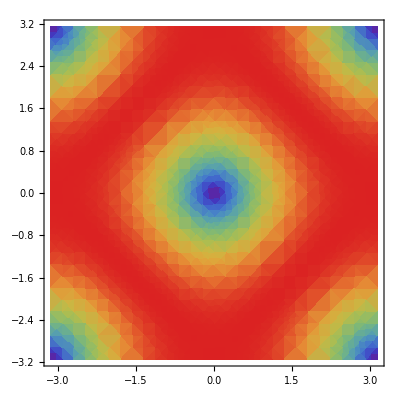

```mathematica
J=1;
DensityPlot[(ϵ[x,y,0.0]),{x,-π,π},{y,-π,π},PlotRange->All,ColorFunction->"Rainbow"]
```

```mathematica
r=0.1;
Manipulate[Plot[ϵ[r*Cos[ϕ],r*Sin[ϕ],0.0],{ϕ,0,2π}],{r,0,π}]
```

```mathematica
Clear[z];
z=4;
Series[ϵ[x,y,b],{y,0,2},{x,0,2}]
```

(64 √(b^2) J+((4 J)/(√(b^2))-12 √(b^2) J) x^2+O[x]^3)+(((4 J)/(√(b^2))-12 √(b^2) J)+(J/(2 √(b^2))-(√(b^2) J)/4-(√(b^2) J)/(4 b^4)) x^2+O[x]^3) y^2+O[y]^3

```mathematica
Series[Cosh[x],{x,0,3}]
```

1+x^2/2+O[x]^4

```mathematica
FullSimplify[D[1/(Exp[β*x]-1),x]]
```

β/(2-2 Cosh[x β])

```mathematica
Series[β/(2-2 Cosh[x β]),{x,0,2}]
```

-1/(β x^2)+β/12-(β^3 x^2)/240+O[x]^3

```mathematica
FullSimplify[(-32 J^4 z^4 (b^2 z+(-2+4 b^2) Cos[x]+(-2+4 b^2) Cos[y])^2 (-2+Cos[2 x]+Cos[2 y]))/(Sin[x]*Sin[y])]
```

-32 J^4 z^4 (b^2 z+(-2+4 b^2) Cos[x]+(-2+4 b^2) Cos[y])^2 (-2+Cos[2 x]+Cos[2 y]) Csc[x] Csc[y]

```mathematica
α=0.01;
τ=0.001;
ω=1;
heatconductivitylist=ParallelTable[Table[{T,α^2*Re[Sum[Sum[heatconductivitydensity[kx,ky,ω,b,1/T,τ],{kx,-π+α,π-α,α}],{ky,-π+α,π-α,α}]]},{T,0.01,1000,10}],{b,0,1,0.25}];
ListPlot[heatconductivitylist]
```

$Aborted

ListPlot::lpn: heatconductivitylist is not a list of numbers or pairs of numbers.

ListPlot[heatconductivitylist]

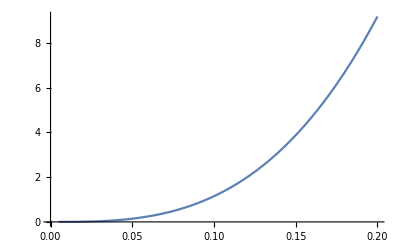

```mathematica
heatconductivitydensity[kx_,ky_,b_,β_,ξ_]:=-(8 J^2 z^2 (z*b^2+γ[kx,ky]*(2*b^2-1)))^2*(Sin[kx]^2+Sin[ky]^2)*(β/2)/(1-Cosh[β*ϵ[kx,ky,b]])*(1)/(2*ξ);
Plot[1/(4π^2)*NIntegrate[heatconductivitydensity[kx,ky,0,1/T,0.001],{kx,-π,π},{ky,-π,π},MaxRecursion->1000,MinRecursion->900,AccuracyGoal->30],{T,0.0,0.2},AxesOrigin->{0,0}]
```

```mathematica
list=Table[{Log[T],Log[NIntegrate[heatconductivitydensity[kx,ky,0,1/T,1],{kx,-π,π},{ky,-π,π},MaxRecursion->1000000000000,MinRecursion->900000000,AccuracyGoal->40]]},{T,0.05,0.2,0.001}];
```

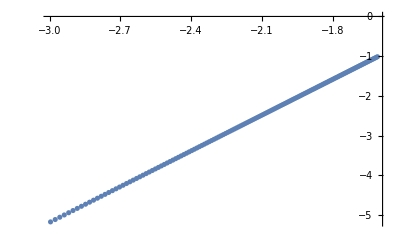

```mathematica
ListPlot[list]
```

```mathematica
Fit[list,{1,x},x]
```

3.81319+2.99983 x

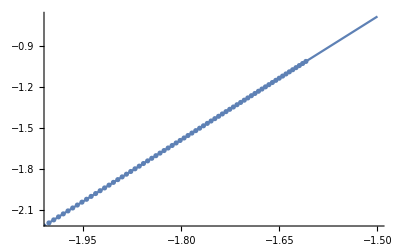

```mathematica
Show[Plot[3.813191441612714+2.9998285011461503 x,{x,-2,-1.5}],ListPlot[list]]
```

```mathematica
Exp[3.8134765354624665]
```

45.3077

```mathematica
Integrate[x^3*Exp[x]/(Exp[x]-1)^2,{x,0,∞}]
```

6 Zeta[3]

```mathematica
N[%]
```

7.21234

```mathematica
45.307679135498326/7.212341418957566
```

6.28197

```mathematica
%*(2π)
```

39.4708

```mathematica
%*2/
```